## first part, n=0

```mathematica
ψk[τ_]:=-I 1/k^(1/2) (  C1 Exp[I k τ] +C2 Exp[-I k τ])
```

```mathematica
ϕk[τ_]:=-I 1/k^(1/2) Exp[I k τ] (1-I α/4/k (1-2 I k (τ-τ1) -Exp[-2 I k (τ-τ1)]))
```

```mathematica
ψk'[τ2]==ϕk'[τ2]//Simplify
```

(ⅇ^(-ⅈ k τ2) (-4 C2 k+ⅈ ⅇ^(2 ⅈ k τ1) α+ⅇ^(2 ⅈ k τ2) (-ⅈ α+2 k (-2+2 C1-α τ1+α τ2))))/(√k)==0

```mathematica
(Solve[{ψk[τ2]==ϕk[τ2],ψk'[τ2]==ϕk'[τ2]},{C1,C2}]//Simplify)/.τ2->Δτ+τ1//Simplify//Flatten
```

{C1→1-(α Δτ)/2,C2→-(ⅈ ⅇ^(2 ⅈ k τ1) (-1+ⅇ^(2 ⅈ k Δτ)) α)/(4 k)}

```mathematica
ψ2k[τ_]:=-I 1/k^(1/2) (  C1 Exp[I k τ] +C2 Exp[-I k τ])/.{C1->1-(α Δτ)/2,C2->-(ⅈ ⅇ^(2 ⅈ k τ1) (-1+ⅇ^(2 ⅈ k Δτ)) α)/(4 k)}//Simplify
```

```mathematica
Collect[ψ2k[τ],α]
```

-(ⅈ ⅇ^(ⅈ k τ))/(√k)+(ⅇ^(-ⅈ k τ) α (ⅇ^(2 ⅈ k τ1)-ⅇ^(2 ⅈ k (Δτ+τ1))+2 ⅈ ⅇ^(2 ⅈ k τ) k Δτ))/(4 k^(3/2))

```mathematica
β2=Normal[Series[(k (1/(4 k^(3/2))ⅇ^(-ⅈ k τ) α (ⅇ^(2 ⅈ k τ1)-ⅇ^(2 ⅈ k (Δτ+τ1))+2 ⅈ ⅇ^(2 ⅈ k τ) k Δτ))(1/(4 k^(3/2))ⅇ^(ⅈ k τ) α (ⅇ^(-2 ⅈ k τ1)-ⅇ^(-2 ⅈ k (Δτ+τ1))-2 ⅈ ⅇ^(-2 ⅈ k τ) k Δτ))//Expand//ExpToTrig//Simplify)/.Δτ->(1+√(1+2 Π1))/α,{α,Infinity,0}]]//FullSimplify
```

(1+√(1+2 Π1))^2 Sin[k (-τ+τ1)]^2

```mathematica
ψ2ks[τ_]:=(ⅈ ⅇ^(-ⅈ k τ))/(√k)+1/(4 k^(3/2))ⅇ^(ⅈ k τ) α (ⅇ^(-2 ⅈ k τ1)-ⅇ^(-2 ⅈ k (Δτ+τ1))-2 ⅈ ⅇ^(-2 ⅈ k τ) k Δτ)
```

```mathematica
Collect[Simplify[Expand[k^3 ψ2k[τ]ψ2ks[τ]//ExpToTrig ]],α]
```

k^2+1/8 α (-8 k^2 Δτ+4 k Sin[2 k (τ-τ1)]-4 k Sin[2 k τ-2 k (Δτ+τ1)])+1/8 α^2 (1+2 k^2 Δτ^2-Cos[2 k Δτ]-2 k Δτ Sin[2 k (τ-τ1)]+2 k Δτ Sin[2 k τ-2 k (Δτ+τ1)])

```mathematica
Solve[(-2+Π0) Π0==2 Π1,Π0]
```

{{Π0→1-√(1+2 Π1)},{Π0→1+√(1+2 Π1)}}

```mathematica
PNEW=Normal[Series[Collect[Simplify[Expand[k^3 ψ2k[τ]ψ2ks[τ]//ExpToTrig ]],α]/.Δτ->(1+√(1+2 Π1))/α,{α,Infinity,0}]]//FullSimplify
```

k^2 (1+Π1-Π1 Cos[2 k (τ-τ1)])

```mathematica
Normal[Series[PNEW,{k,0,2}]]
```

k^2

```mathematica
(Coefficient[I k^(3/2) Exp[-I k τ]Expand[ψ2k[τ]],α]//Expand//FullSimplify)//ExpToTrig
```

1/4 ⅈ (Cos[2 k τ]-ⅈ Sin[2 k τ]) (2 ⅈ k Δτ Cos[2 k τ]+Cos[2 k τ1]-Cos[2 k (Δτ+τ1)]-2 k Δτ Sin[2 k τ]+ⅈ Sin[2 k τ1]-ⅈ Sin[2 k (Δτ+τ1)])

```mathematica
ψ2ks[τ_]:=1/k^(3/2)ⅈ (ⅇ^(ⅈ k τ)+1/(4 k)ⅇ^(-ⅈ k (τ-2 (Δτ+τ1))) α (-ⅈ+ⅈ ⅇ^(-2 ⅈ k Δτ)+2 k Δτ))
```

```mathematica
PS2=Collect[k^3 ψ2k[τ] ψ2ks[τ]//Expand//Simplify,α,FullSimplify]
```

ⅇ^(2 ⅈ k τ) k+(ⅇ^(-2 ⅈ k (τ-τ1)) α^2 (ⅇ^(2 ⅈ k τ1)-ⅇ^(2 ⅈ k (Δτ+τ1))+2 ⅈ ⅇ^(2 ⅈ k τ) k Δτ) (-1+ⅇ^(2 ⅈ k Δτ) (1+2 ⅈ k Δτ)))/(16 k)+1/2 α (ⅈ ⅇ^(2 ⅈ k τ1)-ⅇ^(2 ⅈ k τ) k Δτ+ⅇ^(2 ⅈ k (Δτ+τ1)) (-ⅈ+k Δτ))

```mathematica
PS3=Normal[Series[PS2/.Δτ->Π0/α,{α,Infinity,0}]]/.τ->τ3/.k->κ/(τ1-τ3)
```

(ⅇ^((2 ⅈ κ τ3)/(τ1-τ3)) κ)/(τ1-τ3)-((-3 ⅇ^((2 ⅈ κ τ1)/(τ1-τ3))+ⅇ^((2 ⅈ κ τ3)/(τ1-τ3))) κ Π0)/(2 (τ1-τ3))-(ⅇ^(-(2 ⅈ κ (-τ1+τ3))/(τ1-τ3)) (-ⅇ^((2 ⅈ κ τ1)/(τ1-τ3))+ⅇ^((2 ⅈ κ τ3)/(τ1-τ3))) κ Π0^2)/(2 (τ1-τ3))

```mathematica
LogLogPlot[PS3/.Π0->100,{κ,0,100}]
```

-Graphics-

## second part, n=2

```mathematica
ψk[τ_]:= -(3 H0^2)/II0 1/k^(5/2) (  C1 Exp[-I k τ](1+I k τ-k^2 τ^2/3) +C2 Exp[I k τ](1-I k τ-k^2 τ^2/3) )
```

```mathematica
I2[τ_]:=1/(H0^2 τ^2)
```

```mathematica
ψk[τ]/.C1->1/.C2->0
```

-(3 ⅇ^(-ⅈ k τ) H0^2 (1+ⅈ k τ-(k^2 τ^2)/3))/(II0 k^(5/2))

```mathematica
Simplify[k^3(-(ⅈ ⅇ^(-ⅈ k τ) (1+ⅈ k τ-(k^2 τ^2)/3))/k^(5/2))((ⅈ ⅇ^(ⅈ k τ) (1-ⅈ k τ-(k^2 τ^2)/3))/k^(5/2))  k^2 ]/.τ->0
```

1

```mathematica
ϕk[τ_]:=-3 H0^2/II0   1/k^(5/2) Exp[-I k τ](1+I k τ-k^2 τ^2/3-α/6 k^2 (τ-τ1)^2-I α/12  k τ1 (1+2 I k (τ-τ1) -Exp[2 I k (τ-τ1)]))
```

```mathematica
ϕk[τ2]
```

-(3 ⅇ^(-ⅈ k τ2) H0^2 (1+ⅈ k τ2-(k^2 τ2^2)/3-1/6 k^2 α (-τ1+τ2)^2-1/12 ⅈ k α τ1 (1-ⅇ^(2 ⅈ k (-τ1+τ2))+2 ⅈ k (-τ1+τ2))))/(II0 k^(5/2))

```mathematica
ψk'[τ2]==ϕk'[τ2]//Simplify
```

(ⅇ^(-ⅈ k τ2) H0 (4 τ2 (1+ⅈ k τ2+C1 (-1-ⅈ k τ2)+ⅈ C2 ⅇ^(2 ⅈ k τ2) (ⅈ+k τ2))+α (4 ⅈ k τ1^2-τ1 (-5+ⅇ^(2 ⅈ k (-τ1+τ2))+6 ⅈ k τ2)+2 ⅈ τ2 (2 ⅈ+k τ2))))/(II0 √k)==0

```mathematica
solC=(Solve[{ψk[τ2]==ϕk[τ2],ψk'[τ2]==ϕk'[τ2]},{C1,C2}]//Simplify)//FullSimplify//Flatten
```

{C1→1+(α (4 k τ1^2 (-3+2 k τ2 (2 ⅈ+k τ2))+2 τ2 (-6 ⅈ+k τ2 (-9+2 k τ2 (3 ⅈ+k τ2)))+τ1 (15 ⅈ-ⅇ^(2 ⅈ k (-τ1+τ2)) (3 ⅈ+2 k τ2)-4 k τ2 (-8+k τ2 (7 ⅈ+3 k τ2)))))/(8 k^3 τ2^4),C2→(ⅇ^(-2 ⅈ k τ2) α (4 k τ1^2 (3+2 ⅈ k τ2)-6 τ2 (-2 ⅈ+k τ2)-ⅈ τ1 (15+2 k τ2 (-ⅈ+3 k τ2)+ⅇ^(2 ⅈ k (-τ1+τ2)) (-3+2 k τ2 (-2 ⅈ+k τ2)))))/(8 k^3 τ2^4)}

```mathematica
(Collect[solC[[1,2]],α]//ExpToTrig)/.τ2->τ1-τ1 Δτ/.k->-κ/τ1 //FullSimplify
```

1+(α (-3 ⅈ+2 κ+ⅇ^(2 ⅈ Δτ κ) (3 ⅈ+2 (-1+Δτ) κ)+2 Δτ (-6 ⅈ+κ (2-9 Δτ+2 ⅈ (-1+Δτ) (1+3 Δτ) κ+2 (-1+Δτ)^2 (1+Δτ) κ^2))))/(8 (-1+Δτ)^4 κ^3)

```mathematica
(Collect[solC[[2,2]],α]//ExpToTrig)/.τ2->τ1-τ1 Δτ/.k->-κ/τ1 //FullSimplify
```

(ⅇ^(-ⅈ (-2+Δτ) κ) α (Δτ (6 ⅈ+κ (9-3 Δτ+4 ⅈ (-1+Δτ) κ)) Cos[Δτ κ]+(3+6 Δτ+ⅈ (-4+Δτ (-5+3 Δτ)) κ+2 (-1+Δτ^2) κ^2) Sin[Δτ κ]))/(4 (-1+Δτ)^4 κ^3)

```mathematica
D[ψk[τ],τ]//Simplify
```

(ⅈ ⅇ^(-ⅈ k τ) H0^2 τ (C1 (ⅈ-k τ)+C2 ⅇ^(2 ⅈ k τ) (ⅈ+k τ)))/(II0 √k)

```mathematica
ψN=((D[ψk[τ],τ]/.τ2->τ1-τ1 Δτ/.k->-κ/τ1 //Simplify)//ExpToTrig//Expand//Simplify)
```

(H0^2 τ √(-κ/τ1) ((C1 (-ⅈ κ τ+τ1)+C2 (ⅈ κ τ+τ1)) Cos[(κ τ)/τ1]+(C1 κ τ+C2 κ τ+ⅈ C1 τ1-ⅈ C2 τ1) Sin[(κ τ)/τ1]))/(II0 κ)

```mathematica
ψk[0]
```

```mathematica
ψ0=(ψk[0]/.solC/.τ2->τ1-τ1 Δτ/.k->-κ/τ1 //FullSimplify)//ExpToTrig//Expand//FullSimplify
```

1/(8 II0 (-1+Δτ)^4 κ^6)3 H0^2 (8 (-1+Δτ)^4 κ^3+ⅇ^(2 ⅈ Δτ κ) α (3 ⅈ+2 (-1+Δτ) κ)+ⅇ^(-2 ⅈ (-1+Δτ) κ) α (3 ⅈ (1+4 Δτ)+2 (2+(7-3 Δτ) Δτ) κ+2 ⅈ (-1+Δτ) (1+3 Δτ) κ^2)+ⅇ^(2 ⅈ κ) α (-3 ⅈ+2 (-1+Δτ) κ (2+ⅈ (-1+Δτ) κ))+α (-3 ⅈ+2 κ+2 Δτ (-6 ⅈ+κ (2-9 Δτ+2 ⅈ (-1+Δτ) (1+3 Δτ) κ+2 (-1+Δτ)^2 (1+Δτ) κ^2)))) √(-κ/τ1) τ1^3

```mathematica
ψ0s=(3 H0^2 (8 (-1+Δτ)^4 κ^3+ⅇ^(-2 ⅈ Δτ κ) α (-3 ⅈ+2 (-1+Δτ) κ)+ⅇ^(2 ⅈ (-1+Δτ) κ) α (-3 ⅈ (1+4 Δτ)+2 (2+(7-3 Δτ) Δτ) κ-2 ⅈ (-1+Δτ) (1+3 Δτ) κ^2)+ⅇ^(-2 ⅈ κ) α (3 ⅈ+2 (-1+Δτ) κ (2-ⅈ (-1+Δτ) κ))+α (3 ⅈ+2 κ+2 Δτ (6 ⅈ+κ (2-9 Δτ-2 ⅈ (-1+Δτ) (1+3 Δτ) κ+2 (-1+Δτ)^2 (1+Δτ) κ^2)))) √(-κ/τ1) τ1^3)/(8 II0 (-1+Δτ)^4 κ^6)
```

1/(8 II0 (-1+Δτ)^4 κ^6)3 H0^2 (8 (-1+Δτ)^4 κ^3+ⅇ^(-2 ⅈ Δτ κ) α (-3 ⅈ+2 (-1+Δτ) κ)+ⅇ^(2 ⅈ (-1+Δτ) κ) α (-3 ⅈ (1+4 Δτ)+2 (2+(7-3 Δτ) Δτ) κ-2 ⅈ (-1+Δτ) (1+3 Δτ) κ^2)+ⅇ^(-2 ⅈ κ) α (3 ⅈ+2 (-1+Δτ) κ (2-ⅈ (-1+Δτ) κ))+α (3 ⅈ+2 κ+2 Δτ (6 ⅈ+κ (2-9 Δτ-2 ⅈ (-1+Δτ) (1+3 Δτ) κ+2 (-1+Δτ)^2 (1+Δτ) κ^2)))) √(-κ/τ1) τ1^3

```mathematica
res1=Collect[(ψ0 ψ0s//Expand//Simplify)//ExpToTrig//Simplify,α,Simplify]
```

-(9 H0^4 τ1^5)/(II0^2 κ^5)+1/(8 II0^2 (-1+Δτ)^4 κ^8)9 H0^4 α τ1^5 (Cos[4 Δτ κ]-ⅈ Sin[4 Δτ κ]) (ⅈ (3+4 ⅈ κ-2 κ^2+6 Δτ^2 κ (-ⅈ+κ)+Δτ (12+14 ⅈ κ-4 κ^2)) (Cos[(2-6 Δτ) κ]-ⅈ Sin[(2-6 Δτ) κ])+ⅈ (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[(2-4 Δτ) κ]-ⅈ Sin[(2-4 Δτ) κ])-(-3 ⅈ+2 (-1+Δτ) κ) (Cos[2 Δτ κ]+ⅈ Sin[2 Δτ κ])-4 κ (1-2 Δτ^3 κ^2+2 Δτ^4 κ^2+2 Δτ (1+κ^2)-Δτ^2 (9+2 κ^2)) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])-(3 ⅈ+2 (-1+Δτ) κ) (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])-ⅈ (3-4 ⅈ κ-2 κ^2+6 Δτ^2 κ (ⅈ+κ)-2 Δτ (-6+7 ⅈ κ+2 κ^2)) (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])-ⅈ (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ]))+1/(64 II0^2 (-1+Δτ)^8 κ^11)9 H0^4 α^2 τ1^5 (Cos[4 Δτ κ]-ⅈ Sin[4 Δτ κ]) ((-9+18 ⅈ κ+14 κ^2+12 Δτ^3 (1-ⅈ κ) κ^2-4 ⅈ κ^3+2 ⅈ Δτ^2 κ (-21+29 ⅈ κ+10 κ^2)+4 Δτ (-9+15 ⅈ κ+8 κ^2-ⅈ κ^3)) (Cos[2 κ]+ⅈ Sin[2 κ])+(-9-18 ⅈ κ+14 κ^2+12 Δτ^3 (1+ⅈ κ) κ^2+4 ⅈ κ^3+2 Δτ^2 κ (21 ⅈ-29 κ-10 ⅈ κ^2)+4 Δτ (-9-15 ⅈ κ+8 κ^2+ⅈ κ^3)) (Cos[(2-8 Δτ) κ]-ⅈ Sin[(2-8 Δτ) κ])+2 ⅈ (-9 ⅈ+18 κ+14 ⅈ κ^2-4 κ^3+12 Δτ^6 κ^4 (-ⅈ+κ)+4 Δτ^5 κ^3 (15+19 ⅈ κ-5 κ^2)-2 Δτ^4 κ^2 (-63 ⅈ+90 κ+28 ⅈ κ^2+4 κ^3)+4 Δτ^3 κ (-36-51 ⅈ κ+10 κ^2-14 ⅈ κ^3+6 κ^4)+Δτ (-36 ⅈ+54 κ+20 ⅈ κ^2+12 κ^3+12 ⅈ κ^4-4 κ^5)-4 Δτ^2 (18 ⅈ-18 κ+7 ⅈ κ^2-18 κ^3-9 ⅈ κ^4+κ^5)) (Cos[(2-6 Δτ) κ]-ⅈ Sin[(2-6 Δτ) κ])+ⅈ (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (-3 ⅈ+2 κ+4 Δτ^4 κ^3-4 Δτ^3 κ^2 (-3 ⅈ+κ)-2 Δτ^2 κ (9+4 ⅈ κ+2 κ^2)+4 Δτ (-3 ⅈ+κ-ⅈ κ^2+κ^3)) (Cos[(2-4 Δτ) κ]-ⅈ Sin[(2-4 Δτ) κ])-2 (-9-4 κ^2-2 κ^4+4 Δτ^5 κ^4-2 Δτ^4 κ^3 (-6 ⅈ+κ)-4 Δτ^3 κ^3 (7 ⅈ+4 κ)+10 Δτ^2 κ (3 ⅈ+2 κ+2 ⅈ κ^2+2 κ^3)-2 Δτ (18-3 ⅈ κ+8 κ^2+2 ⅈ κ^3+2 κ^4)) (Cos[2 Δτ κ]+ⅈ Sin[2 Δτ κ])-4 (9+4 κ^2+2 κ^4-4 Δτ^6 κ^6-8 Δτ^7 κ^6+4 Δτ^8 κ^6+4 Δτ^5 κ^4 (-1+4 κ^2)+4 Δτ (9+4 κ^2+κ^4)-4 Δτ^3 κ^2 (3+12 κ^2+2 κ^4)+Δτ^4 (18 κ^2+34 κ^4-4 κ^6)+2 Δτ^2 (36+23 κ^2+6 κ^4+2 κ^6)) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])+2 (9+4 κ^2+2 κ^4-4 Δτ^5 κ^4+2 Δτ^4 κ^3 (6 ⅈ+κ)+4 Δτ^3 κ^3 (-7 ⅈ+4 κ)-10 Δτ^2 κ (-3 ⅈ+2 κ-2 ⅈ κ^2+2 κ^3)+2 Δτ (18+3 ⅈ κ+8 κ^2-2 ⅈ κ^3+2 κ^4)) (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])-2 ⅈ (9 ⅈ+18 κ-14 ⅈ κ^2-4 κ^3+12 Δτ^6 κ^4 (ⅈ+κ)-4 Δτ^5 κ^3 (-15+19 ⅈ κ+5 κ^2)-2 Δτ^4 κ^2 (63 ⅈ+90 κ-28 ⅈ κ^2+4 κ^3)+4 Δτ^3 κ (-36+51 ⅈ κ+10 κ^2+14 ⅈ κ^3+6 κ^4)-4 Δτ^2 (-18 ⅈ-18 κ-7 ⅈ κ^2-18 κ^3+9 ⅈ κ^4+κ^5)-2 Δτ (-18 ⅈ-27 κ+10 ⅈ κ^2-6 κ^3+6 ⅈ κ^4+2 κ^5)) (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])-ⅈ (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (3 ⅈ+2 κ+4 Δτ^4 κ^3-4 Δτ^3 κ^2 (3 ⅈ+κ)-2 Δτ^2 κ (9-4 ⅈ κ+2 κ^2)+4 Δτ (3 ⅈ+κ+ⅈ κ^2+κ^3)) (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ]))

```mathematica
Normal[Series[res1,{κ,0,-5}]]
```

-(9 H0^4 τ1^5)/(II0^2 κ^5)

```mathematica
pow1=res1/Normal[Series[res1,{κ,0,-5}]];
```

```mathematica
Normal[Series[pow1,{κ,0,2}]]
```

1-1/15 α (2 Δτ+3 Δτ^2) κ^2

```mathematica
pow2=Collect[(Collect[pow1,α]//TrigToExp//Expand//Simplify)//ExpToTrig,α,Simplify]
```

1+1/(8 (-1+Δτ)^4 κ^3)α (Cos[2 (1+2 Δτ) κ]-ⅈ Sin[2 (1+2 Δτ) κ]) ((3 ⅈ+4 (-1+Δτ) κ-2 ⅈ (-1+Δτ)^2 κ^2) Cos[4 Δτ κ]+(-3 ⅈ+4 κ+2 ⅈ κ^2-6 ⅈ Δτ^2 κ (-ⅈ+κ)+2 Δτ (-6 ⅈ+7 κ+2 ⅈ κ^2)) Cos[6 Δτ κ]-3 ⅈ Cos[2 (1+Δτ) κ]-2 κ Cos[2 (1+Δτ) κ]+2 Δτ κ Cos[2 (1+Δτ) κ]-3 ⅈ Cos[4 (1+Δτ) κ]-4 κ Cos[4 (1+Δτ) κ]+4 Δτ κ Cos[4 (1+Δτ) κ]+2 ⅈ κ^2 Cos[4 (1+Δτ) κ]-4 ⅈ Δτ κ^2 Cos[4 (1+Δτ) κ]+2 ⅈ Δτ^2 κ^2 Cos[4 (1+Δτ) κ]+3 ⅈ Cos[2 (2+Δτ) κ]+12 ⅈ Δτ Cos[2 (2+Δτ) κ]+4 κ Cos[2 (2+Δτ) κ]+14 Δτ κ Cos[2 (2+Δτ) κ]-6 Δτ^2 κ Cos[2 (2+Δτ) κ]-2 ⅈ κ^2 Cos[2 (2+Δτ) κ]-4 ⅈ Δτ κ^2 Cos[2 (2+Δτ) κ]+6 ⅈ Δτ^2 κ^2 Cos[2 (2+Δτ) κ]+4 κ Cos[2 (1+2 Δτ) κ]+8 Δτ κ Cos[2 (1+2 Δτ) κ]-36 Δτ^2 κ Cos[2 (1+2 Δτ) κ]+8 Δτ κ^3 Cos[2 (1+2 Δτ) κ]-8 Δτ^2 κ^3 Cos[2 (1+2 Δτ) κ]-8 Δτ^3 κ^3 Cos[2 (1+2 Δτ) κ]+8 Δτ^4 κ^3 Cos[2 (1+2 Δτ) κ]+3 ⅈ Cos[2 (1+3 Δτ) κ]-2 κ Cos[2 (1+3 Δτ) κ]+2 Δτ κ Cos[2 (1+3 Δτ) κ]-3 Sin[4 Δτ κ]-4 ⅈ κ Sin[4 Δτ κ]+4 ⅈ Δτ κ Sin[4 Δτ κ]+2 κ^2 Sin[4 Δτ κ]-4 Δτ κ^2 Sin[4 Δτ κ]+2 Δτ^2 κ^2 Sin[4 Δτ κ]+3 Sin[6 Δτ κ]+12 Δτ Sin[6 Δτ κ]+4 ⅈ κ Sin[6 Δτ κ]+14 ⅈ Δτ κ Sin[6 Δτ κ]-6 ⅈ Δτ^2 κ Sin[6 Δτ κ]-2 κ^2 Sin[6 Δτ κ]-4 Δτ κ^2 Sin[6 Δτ κ]+6 Δτ^2 κ^2 Sin[6 Δτ κ]+3 Sin[2 (1+Δτ) κ]-2 ⅈ κ Sin[2 (1+Δτ) κ]+2 ⅈ Δτ κ Sin[2 (1+Δτ) κ]+3 Sin[4 (1+Δτ) κ]-4 ⅈ κ Sin[4 (1+Δτ) κ]+4 ⅈ Δτ κ Sin[4 (1+Δτ) κ]-2 κ^2 Sin[4 (1+Δτ) κ]+4 Δτ κ^2 Sin[4 (1+Δτ) κ]-2 Δτ^2 κ^2 Sin[4 (1+Δτ) κ]-3 Sin[2 (2+Δτ) κ]-12 Δτ Sin[2 (2+Δτ) κ]+4 ⅈ κ Sin[2 (2+Δτ) κ]+14 ⅈ Δτ κ Sin[2 (2+Δτ) κ]-6 ⅈ Δτ^2 κ Sin[2 (2+Δτ) κ]+2 κ^2 Sin[2 (2+Δτ) κ]+4 Δτ κ^2 Sin[2 (2+Δτ) κ]-6 Δτ^2 κ^2 Sin[2 (2+Δτ) κ]+4 ⅈ κ Sin[2 (1+2 Δτ) κ]+8 ⅈ Δτ κ Sin[2 (1+2 Δτ) κ]-36 ⅈ Δτ^2 κ Sin[2 (1+2 Δτ) κ]+8 ⅈ Δτ κ^3 Sin[2 (1+2 Δτ) κ]-8 ⅈ Δτ^2 κ^3 Sin[2 (1+2 Δτ) κ]-8 ⅈ Δτ^3 κ^3 Sin[2 (1+2 Δτ) κ]+8 ⅈ Δτ^4 κ^3 Sin[2 (1+2 Δτ) κ]-3 Sin[2 (1+3 Δτ) κ]-2 ⅈ κ Sin[2 (1+3 Δτ) κ]+2 ⅈ Δτ κ Sin[2 (1+3 Δτ) κ])+1/(64 (-1+Δτ)^8 κ^6)α^2 (Cos[2 (1+2 Δτ) κ]-ⅈ Sin[2 (1+2 Δτ) κ]) ((9-18 ⅈ κ-14 κ^2+4 ⅈ κ^3+12 ⅈ Δτ^3 κ^2 (ⅈ+κ)+2 Δτ^2 κ (21 ⅈ+29 κ-10 ⅈ κ^2)+4 Δτ (9-15 ⅈ κ-8 κ^2+ⅈ κ^3)) (Cos[4 κ]+ⅈ Sin[4 κ])-3 (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])-12 Δτ (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])-2 ⅈ κ (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])-4 ⅈ Δτ κ (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])+18 ⅈ Δτ^2 κ (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])-4 Δτ κ^2 (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])-8 Δτ^2 κ^2 (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])+12 Δτ^3 κ^2 (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])-4 ⅈ Δτ κ^3 (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])+4 ⅈ Δτ^2 κ^3 (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])+4 ⅈ Δτ^3 κ^3 (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])-4 ⅈ Δτ^4 κ^3 (-3+4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 Δτ κ]+ⅈ Sin[4 Δτ κ])-18 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])-72 Δτ (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])-144 Δτ^2 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+288 ⅈ Δτ^3 κ (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+28 κ^2 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+40 Δτ κ^2 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])-56 Δτ^2 κ^2 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])-408 Δτ^3 κ^2 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+252 Δτ^4 κ^2 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+8 ⅈ κ^3 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+360 ⅈ Δτ^4 κ^3 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+24 Δτ κ^4 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+72 Δτ^2 κ^4 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])-112 Δτ^3 κ^4 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])-112 Δτ^4 κ^4 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+152 Δτ^5 κ^4 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])-24 Δτ^6 κ^4 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+8 ⅈ Δτ κ^5 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+8 ⅈ Δτ^2 κ^5 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+16 ⅈ Δτ^4 κ^5 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+40 ⅈ Δτ^5 κ^5 (Cos[6 Δτ κ]+ⅈ Sin[6 Δτ κ])+36 κ (-ⅈ Cos[6 Δτ κ]+Sin[6 Δτ κ])+108 Δτ κ (-ⅈ Cos[6 Δτ κ]+Sin[6 Δτ κ])+144 Δτ^2 κ (-ⅈ Cos[6 Δτ κ]+Sin[6 Δτ κ])+24 Δτ κ^3 (-ⅈ Cos[6 Δτ κ]+Sin[6 Δτ κ])+144 Δτ^2 κ^3 (-ⅈ Cos[6 Δτ κ]+Sin[6 Δτ κ])+80 Δτ^3 κ^3 (-ⅈ Cos[6 Δτ κ]+Sin[6 Δτ κ])+120 Δτ^5 κ^3 (-ⅈ Cos[6 Δτ κ]+Sin[6 Δτ κ])+48 Δτ^3 κ^5 (-ⅈ Cos[6 Δτ κ]+Sin[6 Δτ κ])+24 Δτ^6 κ^5 (-ⅈ Cos[6 Δτ κ]+Sin[6 Δτ κ])+(9+18 ⅈ κ-14 κ^2-4 ⅈ κ^3-12 ⅈ Δτ^3 κ^2 (-ⅈ+κ)+2 Δτ^2 κ (-21 ⅈ+29 κ+10 ⅈ κ^2)+4 Δτ (9+15 ⅈ κ-8 κ^2-ⅈ κ^3)) (Cos[8 Δτ κ]+ⅈ Sin[8 Δτ κ])-18 (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])-72 Δτ (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])+12 ⅈ Δτ κ (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])+60 ⅈ Δτ^2 κ (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])-8 κ^2 (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])-32 Δτ κ^2 (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])+40 Δτ^2 κ^2 (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])+40 ⅈ Δτ^2 κ^3 (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])+24 ⅈ Δτ^4 κ^3 (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])-4 κ^4 (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])-8 Δτ κ^4 (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])+40 Δτ^2 κ^4 (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])-32 Δτ^3 κ^4 (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])-4 Δτ^4 κ^4 (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])+8 Δτ^5 κ^4 (Cos[2 (1+Δτ) κ]+ⅈ Sin[2 (1+Δτ) κ])+8 Δτ κ^3 (-ⅈ Cos[2 (1+Δτ) κ]+Sin[2 (1+Δτ) κ])+56 Δτ^3 κ^3 (-ⅈ Cos[2 (1+Δτ) κ]+Sin[2 (1+Δτ) κ])-3 (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 (1+Δτ) κ]+ⅈ Sin[4 (1+Δτ) κ])-12 Δτ (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 (1+Δτ) κ]+ⅈ Sin[4 (1+Δτ) κ])+2 ⅈ κ (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 (1+Δτ) κ]+ⅈ Sin[4 (1+Δτ) κ])+4 ⅈ Δτ κ (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 (1+Δτ) κ]+ⅈ Sin[4 (1+Δτ) κ])-18 ⅈ Δτ^2 κ (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 (1+Δτ) κ]+ⅈ Sin[4 (1+Δτ) κ])-4 Δτ κ^2 (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 (1+Δτ) κ]+ⅈ Sin[4 (1+Δτ) κ])-8 Δτ^2 κ^2 (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 (1+Δτ) κ]+ⅈ Sin[4 (1+Δτ) κ])+12 Δτ^3 κ^2 (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 (1+Δτ) κ]+ⅈ Sin[4 (1+Δτ) κ])+4 ⅈ Δτ κ^3 (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 (1+Δτ) κ]+ⅈ Sin[4 (1+Δτ) κ])-4 ⅈ Δτ^2 κ^3 (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 (1+Δτ) κ]+ⅈ Sin[4 (1+Δτ) κ])-4 ⅈ Δτ^3 κ^3 (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 (1+Δτ) κ]+ⅈ Sin[4 (1+Δτ) κ])+4 ⅈ Δτ^4 κ^3 (-3-4 ⅈ (-1+Δτ) κ+2 (-1+Δτ)^2 κ^2) (Cos[4 (1+Δτ) κ]+ⅈ Sin[4 (1+Δτ) κ])-18 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])-72 Δτ (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])-144 Δτ^2 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+36 ⅈ κ (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+108 ⅈ Δτ κ (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+144 ⅈ Δτ^2 κ (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+28 κ^2 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+40 Δτ κ^2 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])-56 Δτ^2 κ^2 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])-408 Δτ^3 κ^2 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+252 Δτ^4 κ^2 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+24 ⅈ Δτ κ^3 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+144 ⅈ Δτ^2 κ^3 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+80 ⅈ Δτ^3 κ^3 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+120 ⅈ Δτ^5 κ^3 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+24 Δτ κ^4 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+72 Δτ^2 κ^4 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])-112 Δτ^3 κ^4 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])-112 Δτ^4 κ^4 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+152 Δτ^5 κ^4 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])-24 Δτ^6 κ^4 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+48 ⅈ Δτ^3 κ^5 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+24 ⅈ Δτ^6 κ^5 (Cos[2 (2+Δτ) κ]+ⅈ Sin[2 (2+Δτ) κ])+288 Δτ^3 κ (-ⅈ Cos[2 (2+Δτ) κ]+Sin[2 (2+Δτ) κ])+8 κ^3 (-ⅈ Cos[2 (2+Δτ) κ]+Sin[2 (2+Δτ) κ])+360 Δτ^4 κ^3 (-ⅈ Cos[2 (2+Δτ) κ]+Sin[2 (2+Δτ) κ])+8 Δτ κ^5 (-ⅈ Cos[2 (2+Δτ) κ]+Sin[2 (2+Δτ) κ])+8 Δτ^2 κ^5 (-ⅈ Cos[2 (2+Δτ) κ]+Sin[2 (2+Δτ) κ])+16 Δτ^4 κ^5 (-ⅈ Cos[2 (2+Δτ) κ]+Sin[2 (2+Δτ) κ])+40 Δτ^5 κ^5 (-ⅈ Cos[2 (2+Δτ) κ]+Sin[2 (2+Δτ) κ])+36 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+144 Δτ (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+288 Δτ^2 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+16 κ^2 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+64 Δτ κ^2 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+184 Δτ^2 κ^2 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])-48 Δτ^3 κ^2 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+72 Δτ^4 κ^2 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+8 κ^4 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+16 Δτ κ^4 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+48 Δτ^2 κ^4 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])-192 Δτ^3 κ^4 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+136 Δτ^4 κ^4 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])-16 Δτ^5 κ^4 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+16 Δτ^2 κ^6 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])-32 Δτ^3 κ^6 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])-16 Δτ^4 κ^6 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+64 Δτ^5 κ^6 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])-16 Δτ^6 κ^6 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])-32 Δτ^7 κ^6 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])+16 Δτ^8 κ^6 (Cos[2 (1+2 Δτ) κ]+ⅈ Sin[2 (1+2 Δτ) κ])-18 (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])-72 Δτ (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])-8 κ^2 (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])-32 Δτ κ^2 (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])+40 Δτ^2 κ^2 (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])+8 ⅈ Δτ κ^3 (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])+56 ⅈ Δτ^3 κ^3 (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])-4 κ^4 (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])-8 Δτ κ^4 (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])+40 Δτ^2 κ^4 (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])-32 Δτ^3 κ^4 (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])-4 Δτ^4 κ^4 (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])+8 Δτ^5 κ^4 (Cos[2 (1+3 Δτ) κ]+ⅈ Sin[2 (1+3 Δτ) κ])+12 Δτ κ (-ⅈ Cos[2 (1+3 Δτ) κ]+Sin[2 (1+3 Δτ) κ])+60 Δτ^2 κ (-ⅈ Cos[2 (1+3 Δτ) κ]+Sin[2 (1+3 Δτ) κ])+40 Δτ^2 κ^3 (-ⅈ Cos[2 (1+3 Δτ) κ]+Sin[2 (1+3 Δτ) κ])+24 Δτ^4 κ^3 (-ⅈ Cos[2 (1+3 Δτ) κ]+Sin[2 (1+3 Δτ) κ]))

```mathematica
pow2/.Δτ->0.1/.α->1000/.κ->3
```

16009.6-3.42456×10^-11 ⅈ

```mathematica
pow2a=Simplify[pow2/.Δτ->0.1/.α->1000]
```

1+1/κ^3 135.802 (Cos[2.4 κ]-(0.+1. ⅈ) Sin[2.4 κ]) (((0.+4.20875 ⅈ)-5.05051 κ-(0.+2.27273 ⅈ) κ^2) Cos[0.4 κ]+((0.-5.89226 ⅈ)+7.49158 κ+(0.+3.28283 ⅈ) κ^2) Cos[0.6 κ]-(0.+4.20875 ⅈ) Cos[2.2 κ]-2.52525 κ Cos[2.2 κ]+6.22896 κ Cos[2.4 κ]+1. κ^3 Cos[2.4 κ]+(0.+4.20875 ⅈ) Cos[2.6 κ]-2.52525 κ Cos[2.6 κ]+(0.+5.89226 ⅈ) Cos[4.2 κ]+7.49158 κ Cos[4.2 κ]-(0.+3.28283 ⅈ) κ^2 Cos[4.2 κ]-(0.+4.20875 ⅈ) Cos[4.4 κ]-5.05051 κ Cos[4.4 κ]+(0.+2.27273 ⅈ) κ^2 Cos[4.4 κ]-4.20875 Sin[0.4 κ]-(0.+5.05051 ⅈ) κ Sin[0.4 κ]+2.27273 κ^2 Sin[0.4 κ]+5.89226 Sin[0.6 κ]+(0.+7.49158 ⅈ) κ Sin[0.6 κ]-3.28283 κ^2 Sin[0.6 κ]+4.20875 Sin[2.2 κ]-(0.+2.52525 ⅈ) κ Sin[2.2 κ]+(0.+6.22896 ⅈ) κ Sin[2.4 κ]+(0.+1. ⅈ) κ^3 Sin[2.4 κ]-4.20875 Sin[2.6 κ]-(0.+2.52525 ⅈ) κ Sin[2.6 κ]-5.89226 Sin[4.2 κ]+(0.+7.49158 ⅈ) κ Sin[4.2 κ]+3.28283 κ^2 Sin[4.2 κ]+4.20875 Sin[4.4 κ]-(0.+5.05051 ⅈ) κ Sin[4.4 κ]-2.27273 κ^2 Sin[4.4 κ])+1/κ^6 4610.58 (Cos[2.4 κ]-(0.+1. ⅈ) Sin[2.4 κ]) ((99.1962+(0.+171.468 ⅈ) κ-105.431 κ^2-(0.+6.63198 ⅈ) κ^3-16.0698 κ^4-(0.+4.54545 ⅈ) κ^5) Cos[0.4 κ]+(-209.729-(0.+377.512 ⅈ) κ+244.505 κ^2+(0.+32.3947 ⅈ) κ^3+23.6047 κ^4+(0.+6.56566 ⅈ) κ^5) Cos[0.6 κ]+99.1962 Cos[0.8 κ]+(0.+185.639 ⅈ) κ Cos[0.8 κ]-130.939 κ^2 Cos[0.8 κ]-(0.+33.1599 ⅈ) κ^3 Cos[0.8 κ]-198.392 Cos[2.2 κ]+(0.+14.1709 ⅈ) κ Cos[2.2 κ]-85.0253 κ^2 Cos[2.2 κ]-(0.+3.57106 ⅈ) κ^3 Cos[2.2 κ]-34.8944 κ^4 Cos[2.2 κ]+419.458 Cos[2.4 κ]+190.513 κ^2 Cos[2.4 κ]+77.9512 κ^4 Cos[2.4 κ]+1. κ^6 Cos[2.4 κ]-198.392 Cos[2.6 κ]-(0.+14.1709 ⅈ) κ Cos[2.6 κ]-85.0253 κ^2 Cos[2.6 κ]+(0.+3.57106 ⅈ) κ^3 Cos[2.6 κ]-34.8944 κ^4 Cos[2.6 κ]+99.1962 Cos[4 κ]-(0.+185.639 ⅈ) κ Cos[4 κ]-130.939 κ^2 Cos[4 κ]+(0.+33.1599 ⅈ) κ^3 Cos[4 κ]-209.729 Cos[4.2 κ]+(0.+377.512 ⅈ) κ Cos[4.2 κ]+244.505 κ^2 Cos[4.2 κ]-(0.+32.3947 ⅈ) κ^3 Cos[4.2 κ]+23.6047 κ^4 Cos[4.2 κ]-(0.+6.56566 ⅈ) κ^5 Cos[4.2 κ]+99.1962 Cos[4.4 κ]-(0.+171.468 ⅈ) κ Cos[4.4 κ]-105.431 κ^2 Cos[4.4 κ]+(0.+6.63198 ⅈ) κ^3 Cos[4.4 κ]-16.0698 κ^4 Cos[4.4 κ]+(0.+4.54545 ⅈ) κ^5 Cos[4.4 κ]+(0.+99.1962 ⅈ) Sin[0.4 κ]-171.468 κ Sin[0.4 κ]-(0.+105.431 ⅈ) κ^2 Sin[0.4 κ]+6.63198 κ^3 Sin[0.4 κ]-(0.+16.0698 ⅈ) κ^4 Sin[0.4 κ]+4.54545 κ^5 Sin[0.4 κ]-(0.+209.729 ⅈ) Sin[0.6 κ]+377.512 κ Sin[0.6 κ]+(0.+244.505 ⅈ) κ^2 Sin[0.6 κ]-32.3947 κ^3 Sin[0.6 κ]+(0.+23.6047 ⅈ) κ^4 Sin[0.6 κ]-6.56566 κ^5 Sin[0.6 κ]+(0.+99.1962 ⅈ) Sin[0.8 κ]-185.639 κ Sin[0.8 κ]-(0.+130.939 ⅈ) κ^2 Sin[0.8 κ]+33.1599 κ^3 Sin[0.8 κ]-(0.+198.392 ⅈ) Sin[2.2 κ]-14.1709 κ Sin[2.2 κ]-(0.+85.0253 ⅈ) κ^2 Sin[2.2 κ]+3.57106 κ^3 Sin[2.2 κ]-(0.+34.8944 ⅈ) κ^4 Sin[2.2 κ]+(0.+419.458 ⅈ) Sin[2.4 κ]+(0.+190.513 ⅈ) κ^2 Sin[2.4 κ]+(0.+77.9512 ⅈ) κ^4 Sin[2.4 κ]+(0.+1. ⅈ) κ^6 Sin[2.4 κ]-(0.+198.392 ⅈ) Sin[2.6 κ]+14.1709 κ Sin[2.6 κ]-(0.+85.0253 ⅈ) κ^2 Sin[2.6 κ]-3.57106 κ^3 Sin[2.6 κ]-(0.+34.8944 ⅈ) κ^4 Sin[2.6 κ]+(0.+99.1962 ⅈ) Sin[4 κ]+185.639 κ Sin[4 κ]-(0.+130.939 ⅈ) κ^2 Sin[4 κ]-33.1599 κ^3 Sin[4 κ]-(0.+209.729 ⅈ) Sin[4.2 κ]-377.512 κ Sin[4.2 κ]+(0.+244.505 ⅈ) κ^2 Sin[4.2 κ]+32.3947 κ^3 Sin[4.2 κ]+(0.+23.6047 ⅈ) κ^4 Sin[4.2 κ]+6.56566 κ^5 Sin[4.2 κ]+(0.+99.1962 ⅈ) Sin[4.4 κ]+171.468 κ Sin[4.4 κ]-(0.+105.431 ⅈ) κ^2 Sin[4.4 κ]-6.63198 κ^3 Sin[4.4 κ]-(0.+16.0698 ⅈ) κ^4 Sin[4.4 κ]-4.54545 κ^5 Sin[4.4 κ])

```mathematica
pow2b=Simplify[pow2/.Δτ->0.1/.α->-1000];
```

$Aborted

```mathematica
Re[pow2b]/.κ->0.1
```

1.1603

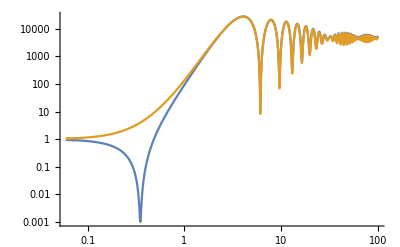

```mathematica
LogLogPlot[{Re[pow2a],Re[pow2b]},{κ,0.06,100}]
```

```mathematica
Normal[Series[pow2,{κ,0,4}]]//Simplify
```

1-1/15 α Δτ (2+3 Δτ) κ^2+1/6300 α Δτ (-360+4 (-360+7 α) Δτ+(40+84 α) Δτ^2+9 (40+7 α) Δτ^3) κ^4

```mathematica
Normal[Series[pow2/.κ->x/(α^(3/12)),{α,Infinity,0}]]//Simplify
```

1/396900(396900-26460 x^2 √α Δτ (2+3 Δτ)+63 x^4 Δτ (-360+4 (-360+7 α) Δτ+(40+84 α) Δτ^2+9 (40+7 α) Δτ^3)-21 x^6 √α Δτ^2 (-72-396 Δτ-613 Δτ^2-168 Δτ^3+24 Δτ^4)+2 x^8 Δτ^2 (-118-496 Δτ-307 Δτ^2+64 Δτ^3-1371 Δτ^4-482 Δτ^5+15 Δτ^6))

```mathematica
pow3=Collect[(Normal[Series[pow2/.Δτ->2 Π0/α,{α,Infinity,0}]]//Expand)//Simplify,{Π0},FullSimplify]
```

1+1/κ^6 4 (1+κ^2) Π0^2 (3 κ Cos[κ]+(-3+κ^2) Sin[κ])^2+1/κ^3 2 Π0 (κ^3-κ (-6+κ^2) Cos[2 κ]+(-3+4 κ^2) Sin[2 κ])

```mathematica
Normal[Series[pow3,{κ,0,2}]]
```

1-(4 κ^2 Π0)/15

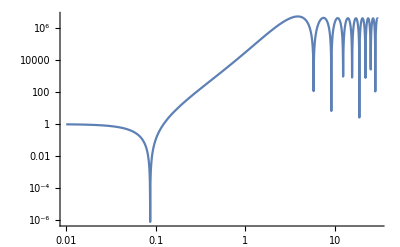

```mathematica
LogLogPlot[(pow3/.Π0->1000),{κ,0.01,30}]
```

```mathematica
Normal[Series[pow3/.κ->1/Sqrt[2] √15 x/Π0^(1/2),{Π0,Infinity,0}]]
```

1-2 x^2+x^4

```mathematica
Solve[(225-30 x^2+x^4)==0,x]
```

{{x→-√15},{x→-√15},{x→√15},{x→√15}}

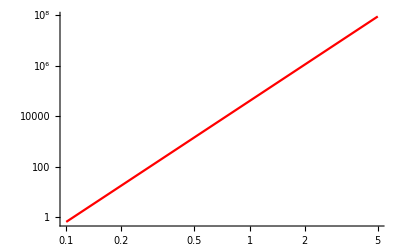

```mathematica
pl=LogLogPlot[{40000 κ^(4.8)},{κ,0.1,5},PlotStyle->{Red}]
```

```mathematica
pl2=LogLogPlot[{(pow3/.Π0->1000)},{κ,0.01,30}]
```

-Graphics-

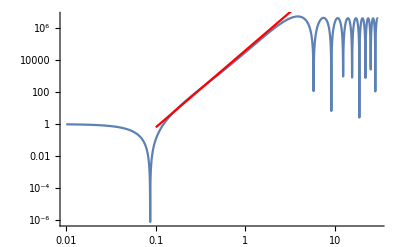

```mathematica
Show[pl2,pl]
```

```mathematica
D[pow3,κ]//Simplify
```

1/κ^7 Π0 (-((27+24 κ^2+4 κ^4) Π0)+(27 Π0-30 κ^2 Π0+κ^6 (8+6 Π0)-2 κ^4 (9+13 Π0)) Cos[2 κ]+κ (54 Π0+κ^6 (2+Π0)+3 κ^2 (3+4 Π0)-κ^4 (16+17 Π0)) Sin[2 κ])

```mathematica
nB=(κ (D[pow3,κ]/.Π0->1000)/(pow3/.Π0->1000))//Simplify;
```

```mathematica
nB/.κ->3
```

(2000 (-1134000+4054374 Cos[6]-2915271 Sin[6]))/(2341458729+899514000 Cos[6]+2161782000 Sin[6])

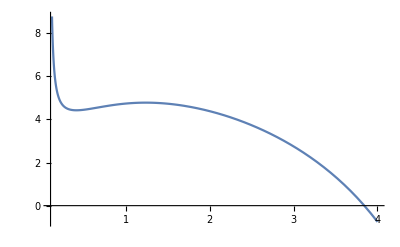

```mathematica
Plot[nB,{κ,0.1,4}]
```

## until here

```mathematica
Coefficient[res1,α]//Expand//FullSimplify
```

(9 H0^4 τ1^5 (2 κ (-1+Δτ (-2+9 Δτ-2 (-1+Δτ)^2 (1+Δτ) κ^2))-3 Sin[2 κ]+2 κ (-2 (-1+Δτ) Cos[2 κ]+(-2+Δτ (-7+3 Δτ)) Cos[2 (-1+Δτ) κ]+(-1+Δτ) (-Cos[2 Δτ κ]+(-1+Δτ) κ Sin[2 κ]))+3 Sin[2 Δτ κ]+3 Sin[2 κ-2 Δτ κ]+2 (6 Δτ+(-1+Δτ) (1+3 Δτ) κ^2) Sin[2 κ-2 Δτ κ]))/(4 II0^2 (-1+Δτ)^4 κ^8)

```mathematica
(*Coefficient[res1,α^2]//Expand//FullSimplify*)
```

$Aborted

```mathematica
res2=1/2187 κ^5 res1/.II0->1/.H0->1/.τ1->-3/.α->5000/.Δτ->0.1//Simplify
```

1+1/κ^3 952.599 (Cos[0.4 κ]-ⅈ Sin[0.4 κ]) ((-3 ⅈ-1.8 κ) (Cos[0.2 κ]+ⅈ Sin[0.2 κ])+0.7128 κ (6.22896+1. κ^2) (Cos[0.4 κ]+(0.+1. ⅈ) Sin[0.4 κ])+(3 ⅈ-1.8 κ) (Cos[0.6 κ]+ⅈ Sin[0.6 κ])+(0.+2.34 ⅈ) (-1.79487-(0.+2.28205 ⅈ) κ+1. κ^2) (Cos[1.4 κ]-(0.+1. ⅈ) Sin[1.4 κ])-ⅈ (-3-(0.+3.6 ⅈ) κ+1.62 κ^2) (Cos[1.6 κ]-ⅈ Sin[1.6 κ])-(0.+2.34 ⅈ) (-1.79487+(0.+2.28205 ⅈ) κ+1. κ^2) (Cos[2.2 κ]+(0.+1. ⅈ) Sin[2.2 κ])+ⅈ (-3+(0.+3.6 ⅈ) κ+1.62 κ^2) (Cos[2.4 κ]+ⅈ Sin[2.4 κ]))+1/κ^6 115264. (Cos[0.4 κ]-(0.+1. ⅈ) Sin[0.4 κ]) ((-198.392+(0.+14.1709 ⅈ) κ-85.0253 κ^2-(0.+3.57106 ⅈ) κ^3-34.8944 κ^4) Cos[0.2 κ]+(419.458+190.513 κ^2+77.9512 κ^4+1. κ^6) Cos[0.4 κ]-198.392 Cos[0.6 κ]-(0.+14.1709 ⅈ) κ Cos[0.6 κ]-85.0253 κ^2 Cos[0.6 κ]+(0.+3.57106 ⅈ) κ^3 Cos[0.6 κ]-34.8944 κ^4 Cos[0.6 κ]+99.1962 Cos[1.2 κ]+(0.+185.639 ⅈ) κ Cos[1.2 κ]-130.939 κ^2 Cos[1.2 κ]-(0.+33.1599 ⅈ) κ^3 Cos[1.2 κ]-209.729 Cos[1.4 κ]-(0.+377.512 ⅈ) κ Cos[1.4 κ]+244.505 κ^2 Cos[1.4 κ]+(0.+32.3947 ⅈ) κ^3 Cos[1.4 κ]+23.6047 κ^4 Cos[1.4 κ]+(0.+6.56566 ⅈ) κ^5 Cos[1.4 κ]+99.1962 Cos[1.6 κ]+(0.+171.468 ⅈ) κ Cos[1.6 κ]-105.431 κ^2 Cos[1.6 κ]-(0.+6.63198 ⅈ) κ^3 Cos[1.6 κ]-16.0698 κ^4 Cos[1.6 κ]-(0.+4.54545 ⅈ) κ^5 Cos[1.6 κ]+99.1962 Cos[2 κ]-(0.+185.639 ⅈ) κ Cos[2 κ]-130.939 κ^2 Cos[2 κ]+(0.+33.1599 ⅈ) κ^3 Cos[2 κ]-209.729 Cos[2.2 κ]+(0.+377.512 ⅈ) κ Cos[2.2 κ]+244.505 κ^2 Cos[2.2 κ]-(0.+32.3947 ⅈ) κ^3 Cos[2.2 κ]+23.6047 κ^4 Cos[2.2 κ]-(0.+6.56566 ⅈ) κ^5 Cos[2.2 κ]+99.1962 Cos[2.4 κ]-(0.+171.468 ⅈ) κ Cos[2.4 κ]-105.431 κ^2 Cos[2.4 κ]+(0.+6.63198 ⅈ) κ^3 Cos[2.4 κ]-16.0698 κ^4 Cos[2.4 κ]+(0.+4.54545 ⅈ) κ^5 Cos[2.4 κ]-(0.+198.392 ⅈ) Sin[0.2 κ]-14.1709 κ Sin[0.2 κ]-(0.+85.0253 ⅈ) κ^2 Sin[0.2 κ]+3.57106 κ^3 Sin[0.2 κ]-(0.+34.8944 ⅈ) κ^4 Sin[0.2 κ]+(0.+419.458 ⅈ) Sin[0.4 κ]+(0.+190.513 ⅈ) κ^2 Sin[0.4 κ]+(0.+77.9512 ⅈ) κ^4 Sin[0.4 κ]+(0.+1. ⅈ) κ^6 Sin[0.4 κ]-(0.+198.392 ⅈ) Sin[0.6 κ]+14.1709 κ Sin[0.6 κ]-(0.+85.0253 ⅈ) κ^2 Sin[0.6 κ]-3.57106 κ^3 Sin[0.6 κ]-(0.+34.8944 ⅈ) κ^4 Sin[0.6 κ]+(0.+198.392 ⅈ) Cos[κ] Sin[κ]+371.277 κ Cos[κ] Sin[κ]-(0.+261.878 ⅈ) κ^2 Cos[κ] Sin[κ]-66.3198 κ^3 Cos[κ] Sin[κ]-(0.+99.1962 ⅈ) Sin[1.2 κ]+185.639 κ Sin[1.2 κ]+(0.+130.939 ⅈ) κ^2 Sin[1.2 κ]-33.1599 κ^3 Sin[1.2 κ]+(0.+209.729 ⅈ) Sin[1.4 κ]-377.512 κ Sin[1.4 κ]-(0.+244.505 ⅈ) κ^2 Sin[1.4 κ]+32.3947 κ^3 Sin[1.4 κ]-(0.+23.6047 ⅈ) κ^4 Sin[1.4 κ]+6.56566 κ^5 Sin[1.4 κ]-(0.+99.1962 ⅈ) Sin[1.6 κ]+171.468 κ Sin[1.6 κ]+(0.+105.431 ⅈ) κ^2 Sin[1.6 κ]-6.63198 κ^3 Sin[1.6 κ]+(0.+16.0698 ⅈ) κ^4 Sin[1.6 κ]-4.54545 κ^5 Sin[1.6 κ]-(0.+209.729 ⅈ) Sin[2.2 κ]-377.512 κ Sin[2.2 κ]+(0.+244.505 ⅈ) κ^2 Sin[2.2 κ]+32.3947 κ^3 Sin[2.2 κ]+(0.+23.6047 ⅈ) κ^4 Sin[2.2 κ]+6.56566 κ^5 Sin[2.2 κ]+(0.+99.1962 ⅈ) Sin[2.4 κ]+171.468 κ Sin[2.4 κ]-(0.+105.431 ⅈ) κ^2 Sin[2.4 κ]-6.63198 κ^3 Sin[2.4 κ]-(0.+16.0698 ⅈ) κ^4 Sin[2.4 κ]-4.54545 κ^5 Sin[2.4 κ])

```mathematica
Re[res2]/.κ->3
```

400177.

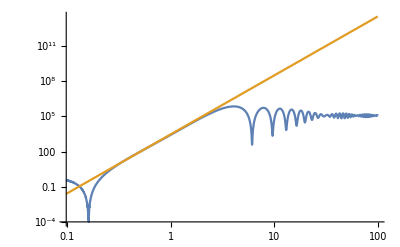

```mathematica
LogLogPlot[{Re[res2],3000 κ^5},{κ,0,100}]
```

```mathematica
Normal[Series[res1,{κ,0,-5}]]
```

-(9 H0^4 τ1^5)/(II0^2 κ^5)

```mathematica
res3=res1/Normal[Series[res1,{κ,0,-5}]]//FullSimplify;
```

$Aborted

```mathematica
gain=Normal[Series[res3,{κ,Infinity,0}]]//FullSimplify
```

(2+Δτ (-4+α+(2+α) Δτ))^2/(4 (-1+Δτ)^4)

```mathematica
Normal[Series[(gain/.Δτ->2Π0/α),{α,Infinity,0}]]
```

(1+Π0)^2

```mathematica
Normal[Series[Normal[Series[res3,{κ,Infinity,0}]],{Δτ,0,10}]]
```

1+α Δτ+(3 α+α^2/4) Δτ^2+Δτ^3 ((3 α^2)/2+16 α κ^2+α (5-16 κ^2))+Δτ^4 (48 α κ^2+4 α^2 κ^2+α (7-48 κ^2)+1/4 α^2 (19-16 κ^2))+Δτ^5 (24 α^2 κ^2+1/4 α^2 (44-96 κ^2)+α (80 κ^2-(256 κ^4)/3)+α (9-80 κ^2+(256 κ^4)/3))+Δτ^6 (α (112 κ^2-256 κ^4)-4/3 α^2 (-57 κ^2+16 κ^4)+1/4 α^2 (85-304 κ^2+(256 κ^4)/3)+α (11-112 κ^2+256 κ^4))+Δτ^7 (1/4 α^2 (704 κ^2-512 κ^4)+1/4 α^2 (146-704 κ^2+512 κ^4)+α (13-144 κ^2+(1280 κ^4)/3-(8192 κ^6)/45)+α (144 κ^2-(1280 κ^4)/3+(8192 κ^6)/45))+Δτ^8 (α (15-176 κ^2+(1792 κ^4)/3-(8192 κ^6)/15)+1/4 α^2 (231-1360 κ^2+(4864 κ^4)/3-(8192 κ^6)/45)+1/4 α^2 (1360 κ^2-(4864 κ^4)/3+(8192 κ^6)/45)+α (176 κ^2-(1792 κ^4)/3+(8192 κ^6)/15))+Δτ^9 (1/4 α^2 (344-2336 κ^2+(11264 κ^4)/3-(16384 κ^6)/15)+1/4 α^2 (2336 κ^2-(11264 κ^4)/3+(16384 κ^6)/15)+α (208 κ^2-768 κ^4+(8192 κ^6)/9-(65536 κ^8)/315)+α (17-208 κ^2+768 κ^4-(8192 κ^6)/9+(65536 κ^8)/315))+Δτ^10 (α (240 κ^2-(2816 κ^4)/3+(57344 κ^6)/45-(65536 κ^8)/105)+1/4 α^2 (3696 κ^2-(21760 κ^4)/3+(155648 κ^6)/45-(65536 κ^8)/315)+1/4 α^2 (489-3696 κ^2+(21760 κ^4)/3-(155648 κ^6)/45+(65536 κ^8)/315)+α (19-240 κ^2+(2816 κ^4)/3-(57344 κ^6)/45+(65536 κ^8)/105))

```mathematica
res5=Collect[Normal[Series[(κ^4 res1/.τ1->-1/.Δτ->2 Π0/α),{α,Infinity,0}]],Π0,FullSimplify]
```

(9 H0^4)/(II0^2 κ)+1/(II0^2 κ^7)36 H0^4 (1+κ^2) Π0^2 (3 κ Cos[κ]+(-3+κ^2) Sin[κ])^2-1/(II0^2 κ^4)18 H0^4 Π0 (-κ^3+κ (-6+κ^2) Cos[2 κ]+(3-4 κ^2) Sin[2 κ])

```mathematica
res6=Collect[Log[κ] (Collect[Integrate[res5,κ],Π0,Simplify])/(Collect[Integrate[res5,κ],Π0,Simplify]/.Π0->0),Π0]
```

Log[κ]-1/κ^3 2 Π0 (2 κ Cos[2 κ]+κ^3 CosIntegral[2 κ]-κ^3 Log[κ]-Sin[2 κ])-1/κ^6 Π0^2 (3+6 κ^2+4 κ^4+(-3+6 κ^4) Cos[2 κ]+2 κ^6 CosIntegral[2 κ]-2 κ^6 Log[κ]-6 κ Sin[2 κ]-8 κ^3 Sin[2 κ])

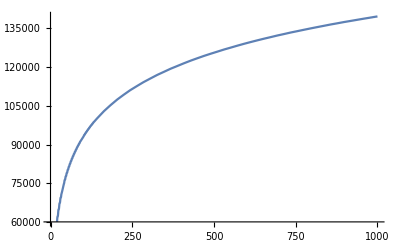

```mathematica
Plot[(res6/.Π0->100),{κ,0.1,1000}]
```

```mathematica
Normal[Series[res6/Log[κ],{κ,Infinity,0}]]
```

1+2 Π0+2 Π0^2

```mathematica
Exp[2 0.2 75]
```

1.06865×10^13

## until here

```mathematica
ψ2k[τ_]:=-I 1/k^(5/2) (  C1 Exp[-I k τ](1+I k τ-k^2 τ^2/3) +C2 Exp[I k τ](1-I k τ-k^2 τ^2/3) )/.{C1->1+1/(8 k^3 τ2^4)α (4 k τ1^2 (-3+2 k τ2 (2 ⅈ+k τ2))+2 τ2 (-6 ⅈ+k τ2 (-9+2 k τ2 (3 ⅈ+k τ2)))+τ1 (15 ⅈ-ⅇ^(2 ⅈ k (-τ1+τ2)) (3 ⅈ+2 k τ2)-4 k τ2 (-8+k τ2 (7 ⅈ+3 k τ2)))),C2->1/(8 k^3 τ2^4)ⅇ^(-2 ⅈ k τ2) α (4 k τ1^2 (3+2 ⅈ k τ2)-6 τ2 (-2 ⅈ+k τ2)-ⅈ τ1 (15+2 k τ2 (-ⅈ+3 k τ2)+ⅇ^(2 ⅈ k (-τ1+τ2)) (-3+2 k τ2 (-2 ⅈ+k τ2))))}//Simplify
```

```mathematica
Collect[ψ2k[τ],α,Simplify]
```

(ⅇ^(-ⅈ k τ) (-3 ⅈ+3 k τ+ⅈ k^2 τ^2))/(3 k^(5/2))-1/(8 k^(11/2) τ2^4)ⅈ α (ⅇ^(ⅈ k (τ-2 τ2)) (1-ⅈ k τ-(k^2 τ^2)/3) (4 k τ1^2 (3+2 ⅈ k τ2)-6 τ2 (-2 ⅈ+k τ2)-ⅈ τ1 (15+2 k τ2 (-ⅈ+3 k τ2)+ⅇ^(2 ⅈ k (-τ1+τ2)) (-3+2 k τ2 (-2 ⅈ+k τ2))))+ⅇ^(-ⅈ k τ) (1+ⅈ k τ-(k^2 τ^2)/3) (4 k τ1^2 (-3+2 k τ2 (2 ⅈ+k τ2))+2 τ2 (-6 ⅈ+k τ2 (-9+2 k τ2 (3 ⅈ+k τ2)))+τ1 (15 ⅈ-ⅇ^(2 ⅈ k (-τ1+τ2)) (3 ⅈ+2 k τ2)-4 k τ2 (-8+k τ2 (7 ⅈ+3 k τ2)))))

```mathematica
ψ2ks[τ_]:=(ⅇ^(ⅈ k τ) (3 ⅈ+3 k τ-ⅈ k^2 τ^2))/(3 k^(5/2))+1/(8 k^(11/2) τ2^4)ⅈ α (ⅇ^(-ⅈ k (τ-2 τ2)) (1+ⅈ k τ-(k^2 τ^2)/3) (4 k τ1^2 (3-2 ⅈ k τ2)-6 τ2 (2 ⅈ+k τ2)+ⅈ τ1 (15+2 k τ2 (ⅈ+3 k τ2)+ⅇ^(-2 ⅈ k (-τ1+τ2)) (-3+2 k τ2 (2 ⅈ+k τ2))))+ⅇ^(ⅈ k τ) (1-ⅈ k τ-(k^2 τ^2)/3) (4 k τ1^2 (-3+2 k τ2 (-2 ⅈ+k τ2))+2 τ2 (6 ⅈ+k τ2 (-9+2 k τ2 (-3 ⅈ+k τ2)))+τ1 (-15 ⅈ-ⅇ^(-2 ⅈ k (-τ1+τ2)) (-3 ⅈ+2 k τ2)-4 k τ2 (-8+k τ2 (-7 ⅈ+3 k τ2)))))
```

```mathematica
pro=Collect[k^5 ψ2ks[0]ψ2k[0]//Simplify//ExpToTrig,α,Simplify]/.τ2->τ1+Δτ
```

1-(α (12 k τ1^2-32 k τ1 (Δτ+τ1)+18 k (Δτ+τ1)^2-8 k^3 τ1^2 (Δτ+τ1)^2+12 k^3 τ1 (Δτ+τ1)^3-4 k^3 (Δτ+τ1)^4+2 k τ1 (Δτ+τ1) Cos[2 k Δτ]+4 k τ1 (Δτ+τ1) Cos[2 k τ1]-12 k τ1^2 Cos[2 k (Δτ+τ1)]+2 k τ1 (Δτ+τ1) Cos[2 k (Δτ+τ1)]+6 k (Δτ+τ1)^2 Cos[2 k (Δτ+τ1)]-3 τ1 Sin[2 k Δτ]-3 τ1 Sin[2 k τ1]+2 k^2 τ1 (Δτ+τ1)^2 Sin[2 k τ1]+15 τ1 Sin[2 k (Δτ+τ1)]-12 (Δτ+τ1) Sin[2 k (Δτ+τ1)]-8 k^2 τ1^2 (Δτ+τ1) Sin[2 k (Δτ+τ1)]+6 k^2 τ1 (Δτ+τ1)^2 Sin[2 k (Δτ+τ1)]))/(4 k^3 (Δτ+τ1)^4)+(α^2 (-2 τ1 (32 k^2 τ1^2 (Δτ+τ1) (-3+2 k^2 (Δτ+τ1)^2)+τ1 (-45+242 k^2 (Δτ+τ1)^2-104 k^4 (Δτ+τ1)^4)+4 (Δτ+τ1) (9-33 k^2 (Δτ+τ1)^2+10 k^4 (Δτ+τ1)^4)) Cos[2 k τ1]-2 τ1 (-45 τ1+36 (Δτ+τ1)+48 k^2 τ1^2 (Δτ+τ1)-22 k^2 τ1 (Δτ+τ1)^2-12 k^2 (Δτ+τ1)^3) Cos[2 k (τ1-2 (Δτ+τ1))]+4 (117 τ1^2+72 k^2 τ1^4-180 τ1 (Δτ+τ1)-144 k^2 τ1^3 (Δτ+τ1)+72 (Δτ+τ1)^2+118 k^2 τ1^2 (Δτ+τ1)^2+32 k^4 τ1^4 (Δτ+τ1)^2-60 k^2 τ1 (Δτ+τ1)^3-48 k^4 τ1^3 (Δτ+τ1)^3+18 k^2 (Δτ+τ1)^4+14 k^4 τ1^2 (Δτ+τ1)^4+16 k^6 τ1^4 (Δτ+τ1)^4+4 k^4 τ1 (Δτ+τ1)^5-48 k^6 τ1^3 (Δτ+τ1)^5+52 k^6 τ1^2 (Δτ+τ1)^6-24 k^6 τ1 (Δτ+τ1)^7+4 k^6 (Δτ+τ1)^8-τ1 (8 k^2 τ1^2 (Δτ+τ1) (3+2 k^2 (Δτ+τ1)^2)+τ1 (45-20 k^2 (Δτ+τ1)^2-18 k^4 (Δτ+τ1)^4)+4 (Δτ+τ1) (-9+k^4 (Δτ+τ1)^4)) Cos[2 k Δτ]+(-48 k^2 τ1^3 (Δτ+τ1) (-3+5 k^2 (Δτ+τ1)^2)+8 k^2 τ1^4 (-9+14 k^2 (Δτ+τ1)^2)-4 τ1 (Δτ+τ1) (-45+75 k^2 (Δτ+τ1)^2+k^4 (Δτ+τ1)^4)-6 (Δτ+τ1)^2 (12-21 k^2 (Δτ+τ1)^2+2 k^4 (Δτ+τ1)^4)+τ1^2 (-117+116 k^2 (Δτ+τ1)^2+144 k^4 (Δτ+τ1)^4)) Cos[2 k (Δτ+τ1)]-36 k τ1^3 Sin[2 k Δτ]+66 k τ1^2 (Δτ+τ1) Sin[2 k Δτ]-30 k τ1 (Δτ+τ1)^2 Sin[2 k Δτ]-8 k^3 τ1^3 (Δτ+τ1)^2 Sin[2 k Δτ]+20 k^3 τ1^2 (Δτ+τ1)^3 Sin[2 k Δτ]-12 k^3 τ1 (Δτ+τ1)^4 Sin[2 k Δτ]-18 k τ1^3 Sin[2 k τ1]+78 k τ1^2 (Δτ+τ1) Sin[2 k τ1]-51 k τ1 (Δτ+τ1)^2 Sin[2 k τ1]+56 k^3 τ1^3 (Δτ+τ1)^2 Sin[2 k τ1]-106 k^3 τ1^2 (Δτ+τ1)^3 Sin[2 k τ1]+48 k^3 τ1 (Δτ+τ1)^4 Sin[2 k τ1]-8 k^5 τ1^3 (Δτ+τ1)^4 Sin[2 k τ1]+12 k^5 τ1^2 (Δτ+τ1)^5 Sin[2 k τ1]-4 k^5 τ1 (Δτ+τ1)^6 Sin[2 k τ1]-234 k τ1^2 (Δτ+τ1) Sin[2 k (Δτ+τ1)]-144 k^3 τ1^4 (Δτ+τ1) Sin[2 k (Δτ+τ1)]+360 k τ1 (Δτ+τ1)^2 Sin[2 k (Δτ+τ1)]+288 k^3 τ1^3 (Δτ+τ1)^2 Sin[2 k (Δτ+τ1)]-144 k (Δτ+τ1)^3 Sin[2 k (Δτ+τ1)]-80 k^3 τ1^2 (Δτ+τ1)^3 Sin[2 k (Δτ+τ1)]+32 k^5 τ1^4 (Δτ+τ1)^3 Sin[2 k (Δτ+τ1)]-120 k^3 τ1 (Δτ+τ1)^4 Sin[2 k (Δτ+τ1)]-72 k^5 τ1^3 (Δτ+τ1)^4 Sin[2 k (Δτ+τ1)]+60 k^3 (Δτ+τ1)^5 Sin[2 k (Δτ+τ1)]+52 k^5 τ1^2 (Δτ+τ1)^5 Sin[2 k (Δτ+τ1)]-12 k^5 τ1 (Δτ+τ1)^6 Sin[2 k (Δτ+τ1)]-18 k τ1^3 Sin[2 k (τ1-2 (Δτ+τ1))]-12 k τ1^2 (Δτ+τ1) Sin[2 k (τ1-2 (Δτ+τ1))]+21 k τ1 (Δτ+τ1)^2 Sin[2 k (τ1-2 (Δτ+τ1))]+8 k^3 τ1^3 (Δτ+τ1)^2 Sin[2 k (τ1-2 (Δτ+τ1))]-6 k^3 τ1^2 (Δτ+τ1)^3 Sin[2 k (τ1-2 (Δτ+τ1))])))/(64 k^6 (Δτ+τ1)^8)

```mathematica
pro2=Collect[Normal[Series[(pro/.Δτ->τ1 ( Π0)/α/.k->κ/τ1),{α,Infinity,0}]]//Simplify,{Π0},FullSimplify]
```

1+1/κ^6(1+κ^2) Π0^2 (3 κ Cos[κ]+(-3+κ^2) Sin[κ])^2+Π0 (-1+(1-6/κ^2) Cos[2 κ]+((3-4 κ^2) Sin[2 κ])/κ^3)

```mathematica
Solve[2-2 c0 c1+c0^2 c1^2==0,c1]
```

{{c1→(1-ⅈ)/c0},{c1→(1+ⅈ)/c0}}

```mathematica
Solve[1-c0 Π0+(c0^2 Π0^2)/2==Π0,c0]//Simplify
```

{{c0→(1-√(-1+2 Π0))/Π0},{c0→(1+√(-1+2 Π0))/Π0}}

```mathematica
Normal[Series[pro2,{κ,Infinity,1}]]
```

Π0+(1+√(-1+2 Π0)) Cos[2 κ]-1/2 (1+√(-1+2 Π0))^2 Cos[2 κ]-(4 (1+√(-1+2 Π0)) Sin[2 κ])/κ+(3 (1+√(-1+2 Π0))^2 Sin[2 κ])/κ

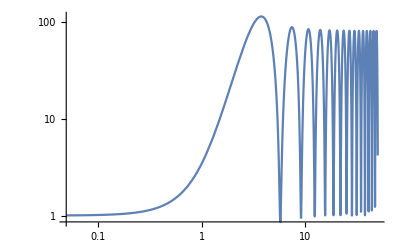

```mathematica
LogLogPlot[pro2/.Π0->10,{κ,0,50}]
```

```mathematica
proa=pro/.Δτ->ΔT τ1/.k->κ/τ1//Simplify
```

1-(α (-2 κ+4 ΔT κ+18 ΔT^2 κ+4 ΔT κ^3+4 ΔT^2 κ^3-4 ΔT^3 κ^3-4 ΔT^4 κ^3+4 (1+ΔT) κ Cos[2 κ]+2 (1+ΔT) κ Cos[2 ΔT κ]-4 κ Cos[2 (1+ΔT) κ]+14 ΔT κ Cos[2 (1+ΔT) κ]+6 ΔT^2 κ Cos[2 (1+ΔT) κ]-3 Sin[2 κ]+2 κ^2 Sin[2 κ]+4 ΔT κ^2 Sin[2 κ]+2 ΔT^2 κ^2 Sin[2 κ]-3 Sin[2 ΔT κ]+3 Sin[2 (1+ΔT) κ]-12 ΔT Sin[2 (1+ΔT) κ]-2 κ^2 Sin[2 (1+ΔT) κ]+4 ΔT κ^2 Sin[2 (1+ΔT) κ]+6 ΔT^2 κ^2 Sin[2 (1+ΔT) κ]))/(4 (1+ΔT)^4 κ^3)+(α^2 (18-72 ΔT+144 ΔT^2+8 κ^2-32 ΔT κ^2+92 ΔT^2 κ^2+24 ΔT^3 κ^2+36 ΔT^4 κ^2+4 κ^4-8 ΔT κ^4+24 ΔT^2 κ^4+96 ΔT^3 κ^4+68 ΔT^4 κ^4+8 ΔT^5 κ^4+8 ΔT^2 κ^6+16 ΔT^3 κ^6-8 ΔT^4 κ^6-32 ΔT^5 κ^6-8 ΔT^6 κ^6+16 ΔT^7 κ^6+8 ΔT^8 κ^6+(9-14 κ^2-96 ΔT^4 κ^4-40 ΔT^5 κ^4+2 ΔT^2 κ^2 (77+16 κ^2)+ΔT^3 (132 κ^2-48 κ^4)+4 ΔT (-9+2 κ^2+6 κ^4)) Cos[2 κ]+(32 ΔT^3 κ^4-4 ΔT^4 κ^4-8 ΔT^5 κ^4+40 ΔT^2 (κ^2+κ^4)+8 ΔT (9+4 κ^2+κ^4)-2 (9+4 κ^2+2 κ^4)) Cos[2 ΔT κ]-18 Cos[2 (1+ΔT) κ]+72 ΔT Cos[2 (1+ΔT) κ]-144 ΔT^2 Cos[2 (1+ΔT) κ]+28 κ^2 Cos[2 (1+ΔT) κ]-40 ΔT κ^2 Cos[2 (1+ΔT) κ]-56 ΔT^2 κ^2 Cos[2 (1+ΔT) κ]+408 ΔT^3 κ^2 Cos[2 (1+ΔT) κ]+252 ΔT^4 κ^2 Cos[2 (1+ΔT) κ]-24 ΔT κ^4 Cos[2 (1+ΔT) κ]+72 ΔT^2 κ^4 Cos[2 (1+ΔT) κ]+112 ΔT^3 κ^4 Cos[2 (1+ΔT) κ]-112 ΔT^4 κ^4 Cos[2 (1+ΔT) κ]-152 ΔT^5 κ^4 Cos[2 (1+ΔT) κ]-24 ΔT^6 κ^4 Cos[2 (1+ΔT) κ]+9 Cos[2 (1+2 ΔT) κ]-36 ΔT Cos[2 (1+2 ΔT) κ]-14 κ^2 Cos[2 (1+2 ΔT) κ]+32 ΔT κ^2 Cos[2 (1+2 ΔT) κ]+58 ΔT^2 κ^2 Cos[2 (1+2 ΔT) κ]+12 ΔT^3 κ^2 Cos[2 (1+2 ΔT) κ]+18 κ Sin[2 κ]-48 ΔT κ Sin[2 κ]-102 ΔT^2 κ Sin[2 κ]-4 κ^3 Sin[2 κ]-28 ΔT κ^3 Sin[2 κ]+52 ΔT^2 κ^3 Sin[2 κ]+172 ΔT^3 κ^3 Sin[2 κ]+96 ΔT^4 κ^3 Sin[2 κ]+8 ΔT κ^5 Sin[2 κ]+24 ΔT^2 κ^5 Sin[2 κ]+16 ΔT^3 κ^5 Sin[2 κ]-16 ΔT^4 κ^5 Sin[2 κ]-24 ΔT^5 κ^5 Sin[2 κ]-8 ΔT^6 κ^5 Sin[2 κ]+12 ΔT κ Sin[2 ΔT κ]-60 ΔT^2 κ Sin[2 ΔT κ]-8 ΔT κ^3 Sin[2 ΔT κ]-40 ΔT^2 κ^3 Sin[2 ΔT κ]-56 ΔT^3 κ^3 Sin[2 ΔT κ]-24 ΔT^4 κ^3 Sin[2 ΔT κ]-36 κ Sin[2 (1+ΔT) κ]+108 ΔT κ Sin[2 (1+ΔT) κ]-144 ΔT^2 κ Sin[2 (1+ΔT) κ]-288 ΔT^3 κ Sin[2 (1+ΔT) κ]+8 κ^3 Sin[2 (1+ΔT) κ]+24 ΔT κ^3 Sin[2 (1+ΔT) κ]-144 ΔT^2 κ^3 Sin[2 (1+ΔT) κ]+80 ΔT^3 κ^3 Sin[2 (1+ΔT) κ]+360 ΔT^4 κ^3 Sin[2 (1+ΔT) κ]+120 ΔT^5 κ^3 Sin[2 (1+ΔT) κ]-8 ΔT κ^5 Sin[2 (1+ΔT) κ]+8 ΔT^2 κ^5 Sin[2 (1+ΔT) κ]+48 ΔT^3 κ^5 Sin[2 (1+ΔT) κ]+16 ΔT^4 κ^5 Sin[2 (1+ΔT) κ]-40 ΔT^5 κ^5 Sin[2 (1+ΔT) κ]-24 ΔT^6 κ^5 Sin[2 (1+ΔT) κ]+18 κ Sin[2 (1+2 ΔT) κ]-60 ΔT κ Sin[2 (1+2 ΔT) κ]-42 ΔT^2 κ Sin[2 (1+2 ΔT) κ]-4 κ^3 Sin[2 (1+2 ΔT) κ]+4 ΔT κ^3 Sin[2 (1+2 ΔT) κ]+20 ΔT^2 κ^3 Sin[2 (1+2 ΔT) κ]+12 ΔT^3 κ^3 Sin[2 (1+2 ΔT) κ]))/(32 (1+ΔT)^8 κ^6)

```mathematica
Normal[Series[proa,{κ,0,2}]]
```

1-1/15 α (-2 ΔT+3 ΔT^2) κ^2

```mathematica
prob=proa/.ΔT->0.1/.α->-1000
```

1+1/κ^3 170.753 (-1.42 κ+0.4356 κ^3+2.2 κ Cos[0.2 κ]+4.4 κ Cos[2 κ]-2.54 κ Cos[2.2 κ]-3 Sin[0.2 κ]-3 Sin[2 κ]+2.42 κ^2 Sin[2 κ]+1.8 Sin[2.2 κ]-1.54 κ^2 Sin[2.2 κ])+1/κ^6 14578.4 (12.24+5.7476 κ^2+3.54288 κ^4+0.0948737 κ^6+(0.03152 κ^4+0.4 (κ^2+κ^4)+0.8 (9+4 κ^2+κ^4)-2 (9+4 κ^2+2 κ^4)) Cos[0.2 κ]+(9-14 κ^2-0.01 κ^4+0.02 κ^2 (77+16 κ^2)+0.001 (132 κ^2-48 κ^4)+0.4 (-9+2 κ^2+6 κ^4)) Cos[2 κ]-12.24 Cos[2.2 κ]+23.8732 κ^2 Cos[2.2 κ]-1.58074 κ^4 Cos[2.2 κ]+5.4 Cos[2.4 κ]-10.208 κ^2 Cos[2.4 κ]+0.6 κ Sin[0.2 κ]-1.2584 κ^3 Sin[0.2 κ]+12.18 κ Sin[2 κ]-6.0984 κ^3 Sin[2 κ]+1.05415 κ^5 Sin[2 κ]-26.928 κ Sin[2.2 κ]+9.0772 κ^3 Sin[2.2 κ]-0.670824 κ^5 Sin[2.2 κ]+11.58 κ Sin[2.4 κ]-3.388 κ^3 Sin[2.4 κ])

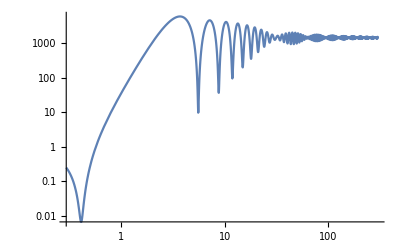

```mathematica
LogLogPlot[prob,{κ,0,300},PlotRange->All]
```

```mathematica
proc=Normal[Series[proa,{κ,Infinity,0}]]//Simplify
```

((2-(-4+α) ΔT+(2+α) ΔT^2)^2)/(4 (1+ΔT)^4)

```mathematica
Normal[Series[proc/.ΔT->2(Π1+1)/α,{α,Infinity,0}]]
```

Π1^2

```mathematica
β2=Normal[Series[(k (1/(4 k^(3/2))ⅇ^(-ⅈ k τ) α (ⅇ^(2 ⅈ k τ1)-ⅇ^(2 ⅈ k (Δτ+τ1))+2 ⅈ ⅇ^(2 ⅈ k τ) k Δτ))(1/(4 k^(3/2))ⅇ^(ⅈ k τ) α (ⅇ^(-2 ⅈ k τ1)-ⅇ^(-2 ⅈ k (Δτ+τ1))-2 ⅈ ⅇ^(-2 ⅈ k τ) k Δτ))//Expand//ExpToTrig//Simplify)/.Δτ->(1+√(1+2 Π1))/α,{α,Infinity,0}]]//FullSimplify
```

(1+√(1+2 Π1))^2 Sin[k (-τ+τ1)]^2

```mathematica
ψ2ks[τ_]:=(ⅈ ⅇ^(-ⅈ k τ))/(√k)+1/(4 k^(3/2))ⅇ^(ⅈ k τ) α (ⅇ^(-2 ⅈ k τ1)-ⅇ^(-2 ⅈ k (Δτ+τ1))-2 ⅈ ⅇ^(-2 ⅈ k τ) k Δτ)
```

```mathematica
Collect[Simplify[Expand[k^3 ψ2k[τ]ψ2ks[τ]//ExpToTrig ]],α]
```

k^2+1/8 α (-8 k^2 Δτ+4 k Sin[2 k (τ-τ1)]-4 k Sin[2 k τ-2 k (Δτ+τ1)])+1/8 α^2 (1+2 k^2 Δτ^2-Cos[2 k Δτ]-2 k Δτ Sin[2 k (τ-τ1)]+2 k Δτ Sin[2 k τ-2 k (Δτ+τ1)])

```mathematica
Solve[(-2+Π0) Π0==2 Π1,Π0]
```

{{Π0→1-√(1+2 Π1)},{Π0→1+√(1+2 Π1)}}

```mathematica
PNEW=Normal[Series[Collect[Simplify[Expand[k^3 ψ2k[τ]ψ2ks[τ]//ExpToTrig ]],α]/.Δτ->(1+√(1+2 Π1))/α,{α,Infinity,0}]]//FullSimplify
```

k^2 (1+Π1-Π1 Cos[2 k (τ-τ1)])

```mathematica
Normal[Series[PNEW,{k,0,2}]]
```

k^2

```mathematica
(Coefficient[I k^(3/2) Exp[-I k τ]Expand[ψ2k[τ]],α]//Expand//FullSimplify)//ExpToTrig
```

1/(4 k)(ⅈ+2 k Δτ-ⅈ Cos[2 k Δτ]+Sin[2 k Δτ]) (Cos[2 k (Δτ+τ1)]-ⅈ Sin[2 k (Δτ+τ1)])

```mathematica
ψ2ks[τ_]:=1/k^(3/2)ⅈ (ⅇ^(ⅈ k τ)+1/(4 k)ⅇ^(-ⅈ k (τ-2 (Δτ+τ1))) α (-ⅈ+ⅈ ⅇ^(-2 ⅈ k Δτ)+2 k Δτ))
```

```mathematica
PS2=Collect[k^3 ψ2k[τ] ψ2ks[τ]//Expand//Simplify,α,FullSimplify]
```

1+1/(8 k^2)α^2 (1+2 k^2 Δτ^2-Cos[2 k Δτ]+2 k Δτ Sin[2 k Δτ])+1/(2 k)α (2 k Δτ Cos[2 k (Δτ-τ+τ1)]+Sin[2 k (τ-τ1)]+Sin[2 k (Δτ-τ+τ1)])

```mathematica
PS3=Normal[Series[PS2/.Δτ->Π0/α,{α,Infinity,0}]]/.τ->τ3/.k->κ/(τ1-τ3)
```

1+Π0^2+2 Π0 Cos[2 κ]

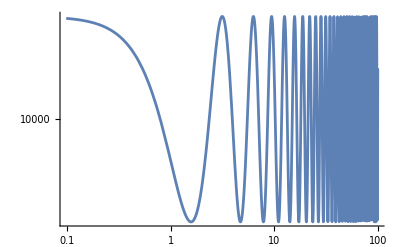

```mathematica
LogLogPlot[PS3/.Π0->100,{κ,0,100}]
```